# Layered BDM as a Texture and Weighted Network Descriptor to Estimate Kolmogorov Complexity

September 3rd, 2016

Author: Antonio Rueda-Toicen

antonio.rueda.toicen@gmail.com

A layered version of the Block Decomposition Method[1], serves as a descriptor of both weighted networks and grayscale or color images.  This descriptor provides an estimate of Kolmogorov Complexity that’s sensitive to morphological perturbative [2].  To estimate the complexity of a grayscale texture, we quantize it and aggregate the estimated Kolmogorov complexity values of binary 4 x 4 squares, estimated through the Coding Theorem Method [3, 4].

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\Antonio Rueda Toicen\Documents\Python\EstimationKolmogorovComplexityImages\ImageAnalysisWithAlgorithmicInformation

```mathematica
data = Import["fourByFourCTMs.csv", "CSV", "Numeric" -> False]
```

{{0000000000000000,22.006706292292176},{0000000000000001,23.347935957593144},{0000000000000010,24.325701071360243},65530,{1111111111111101,24.325701071360243},{1111111111111110,23.347935957593144},{1111111111111111,22.006706292292176}}
 |  |  |  |

```mathematica
fourByFourCTMs = Transpose@{data[[All, 1]], ToExpression /@ data[[All, 2]] };
```

```mathematica
Table[
(CTM[fourByFourCTMs[[i, 1]]] = fourByFourCTMs[[i, 2]]), {i, 1, 65536, 1 }];
```

```mathematica
CTM["0000000000000000"]
```

22.0067

```mathematica
Clear[data, fourByFourCTMs]
```

“Layered BDM” works through the binary quantization of a texture’s digital levels. The examples below quantize textures using 256 digital levels (byte resolution); 2^16, 2^32, etc. quantizations are obviously also possible.

```mathematica
layerDecomposition[image_]:=
 Module[{getLayers, getBlocks, blockCount, stringifiedBlocks}, 
getLayers[imag_] :=ParallelTable[Unitize[ ImageData[ColorConvert[imag, "Grayscale"], "Byte"], i], {i, 1, 255, 1}];
getBlocks[layers_]:= Nest[Flatten[#, 1]&, Partition[#, {4, 4},1]& /@ layers, 2];
blockCount = Tally[getBlocks[getLayers[image]] ]; 
stringifiedBlocks = StringJoin /@ Map[ToString, (Flatten /@ blockCount[[All, 1]]), {2}]; 
Total[CTM /@ stringifiedBlocks] + Total[Log2[blockCount[[All, 2]]]]
]
```

## Layered BDM as a Texture Descriptor

```mathematica
woodTextures = (Image[ColorConvert[#,"Grayscale"], "Byte"]& /@ ImageResize[#, {128, 128}]& /@( ExampleData[#]& /@ {{"Texture","Wood"},{"Texture","Wood2"},{"Texture","Wood3"}}));
```

```mathematica
smallWT = ImageResize[woodTextures[[1]] , {15, 15}]
```

-Graphics-

```mathematica
layerDecomposition[smallWT]
```

28364.8

```mathematica
woodTextures
```

{-Graphics-,-Graphics-,-Graphics-}

BDM seems to align with the intuitive notion of a texture’s complexity.

```mathematica
layerDecomposition /@ woodTextures
```

{457899.,569941.,398956.}

## Test on MR Image with/without an Artifact

```mathematica
t2BrainSlice = Image[ColorConvert[ImageCrop@ -Graphics-,"Grayscale"], "Byte"]
```

-Graphics-

```mathematica
t2BrainSlice // ImageData // Dimensions
```

{185,149}

```mathematica
aImage =ColorNegate@ColorConvert[Image[Rasterize[Style["a", FontSize-> 50]], "Byte"], "Grayscale"]
```

-Graphics-

```mathematica
brainWLetter = Image[ColorConvert[ImageAdd[t2BrainSlice, aImage], "Grayscale"], "Byte" ]
```

-Graphics-

```mathematica
brainWLetter // ImageData // Dimensions
```

{185,149}

The image with a simple texture artifact has lower BDM and lower texture complexity.

```mathematica
layerDecomposition /@ {t2BrainSlice, brainWLetter}
```

{1.39659×10^6,1.38208×10^6}

## Sensitivity to Morphological Perturbation

```mathematica
t2BrainSliceWDiskErosion = Erosion[t2BrainSlice, DiskMatrix[3]]
```

-Graphics-

```mathematica
t2BrainSliceWBoxedErosion = Erosion[t2BrainSlice, BoxMatrix[3]]
```

-Graphics-

LayeredBDM is highly sensitive to morphological perturbations of the data.

```mathematica
layerDecomposition /@ {t2BrainSliceWBoxedErosion, t2BrainSliceWDiskErosion}
```

{59706.4,66779.8}

## Layered BDM as a Weighted Network Descriptor

BDM can be used to evaluate networks trained through backpropagation.

```mathematica
SeedRandom[1];rg = RandomGraph[{10, 30}];
```

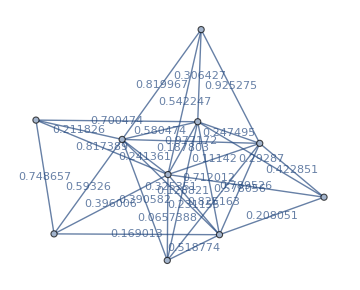
{-Graphics-,-Graphics-}

```mathematica
SeedRandom[1];{wrg = Graph[EdgeList[rg], EdgeWeight-> RandomReal[1, Length[EdgeList[rg]]], EdgeLabels->"EdgeWeight", ImageSize->Medium], ArrayPlot@WeightedAdjacencyMatrix[wrg]}
```

```mathematica
floatToByte[float_] := Floor[If[float === 1.0, 255, float * 256.0]]
```

```mathematica
floatToByte /@ {0.001, 0.999}
```

{0,255}

```mathematica
byteWeightedMatrix = Map[floatToByte, Normal[WeightedAdjacencyMatrix[wrg]], {2}]; MatrixForm[byteWeightedMatrix]
```

(0 | 209 | 28 | 202 | 48 | 61 | 16 | 138 | 59 | 101
209 | 0 | 0 | 0 | 179 | 54 | 0 | 0 | 0 | 191
28 | 0 | 0 | 108 | 63 | 250 | 211 | 236 | 147 | 0
202 | 0 | 108 | 0 | 74 | 0 | 0 | 0 | 53 | 0
48 | 179 | 63 | 74 | 0 | 148 | 32 | 78 | 182 | 0
61 | 54 | 250 | 0 | 148 | 0 | 99 | 209 | 83 | 151
16 | 0 | 211 | 0 | 32 | 99 | 0 | 0 | 132 | 0
138 | 0 | 236 | 0 | 78 | 209 | 0 | 0 | 0 | 0
59 | 0 | 147 | 53 | 182 | 83 | 132 | 0 | 0 | 43
101 | 191 | 0 | 0 | 0 | 151 | 0 | 0 | 43 | 0)

```mathematica
layerDecompositionForWeightedGraphs[weightedGraph_]:=
 Module[{floatToByte, getLayers, getBlocks, blockCount, stringifiedBlocks, weightedAdjMatrix},
floatToByte[float_] := Floor[If[float === 1.0, 255, float * 256.0]]; 
getLayers[w_] :=ParallelTable[Unitize[ Map[floatToByte,weightedAdjMatrix , {2}], i], {i, 1, 255, 1}];
getBlocks[layers_]:= Nest[Flatten[#, 1]&, Partition[#, {4, 4},1]& /@ layers, 2];
weightedAdjMatrix = Normal[WeightedAdjacencyMatrix[weightedGraph]];
blockCount = Tally[getBlocks[getLayers[weightedAdjMatrix]] ]; 
stringifiedBlocks = StringJoin /@ Map[ToString, (Flatten /@ blockCount[[All, 1]]), {2}]; 
Total[CTM /@ stringifiedBlocks] + Total[Log2[blockCount[[All, 2]]]]
]
```

```mathematica
layerDecompositionForWeightedGraphs[wrg]
```

12323.2

## References

[1] Antonio Rueda-Toicen, “Morphological Image Analysis through Estimations of Kolmogorov Complexity” (in preparation)

[2] Hector Zenil, Santiago Hernández - Orozco, Narsis A.Kiani, Fernando Soler - Toscano, Antonio Rueda - Toicen, and Jesper Tegner "A Decomposition Method for Global Evaluation of Shannon Entropy and Local Estimations of Algorithmic Complexity", https://arxiv.org/abs/1609.00110

[3] Fernando Soler - Toscano, Hector Zenil, Jean-Paul Delahaye, and Nicolas Gauvrit (2014) “Calculating Kolmogorov Complexity from the Output Frequency Distributions of Small Turing Machines.” PLoS ONE 9 (5) : e96223.